# Modelos Matemáticos de Linhas de Transmissão Análise de Sistemas de Cabos

## Aluno: Paulo Eduardo Darski Rocha Profs.: Dr. Antonio Carlos Siqueira de Lima / PhD Sandoval Carneiro Jr. Poli/COPPE/UFRJ

## Opções de programa

```mathematica
Clear["Global`*"]
```

```mathematica
SetOptions[{ListPlot,ListLogLinearPlot,ListLogLogPlot},Axes->False,Frame->True,Joined->True,ImageSize->450,PlotStyle->{PointSize[0.015]},BaseStyle->{14,FontFamily->"Helvetica"}];
```

```mathematica
plstyle1={AbsoluteThickness[2],RGBColor[1,0,0]};
plstyle2={AbsoluteThickness[2],RGBColor[0,0,1]};
plstyle3={AbsoluteThickness[2],PointSize[.015],RGBColor[0,1,0]};
```

## Dados de Entrada

Dimensões dos cabos

```mathematica
r1=1.27 10^-2;
r2=2.82 10^-2;
r3=2.93 10^-2;
r4=3.45 10^-2;
```

Constantes Elétricas e Parâmetros do Solo por metro

```mathematica
compr=10*10^3;
μ=4.0 π 10^-7;
ϵ=8.854*10^-12;
ϵcs=3.5;
ϵsg=3.3;
ϵ1=ϵcs ϵ;
ϵ2=ϵsg ϵ;
ρs=1.38 10^-7;
ρc=1.72 10^-8;
ρ=20.0;
```

## Configuração da Rede

Espaçamento dos condutores

```mathematica
x1=1;yc1=-1 ;
x3=x1+r4 ;yc2=-(1+2r4 Sin[Pi/3]);
x5=x1-r4  ;yc3=yc2;
```

```mathematica
xc={x1,x1,x3,x3,x5,x5};
hc={yc1,yc1,yc2,yc2,yc3,yc3};
r={r1,r4,r1,r4,r1,r4};
```

```mathematica
mostra=Table[{Circle[{xc[[i]],hc[[i]]},r[[i]]]},{i,1,6}];
```

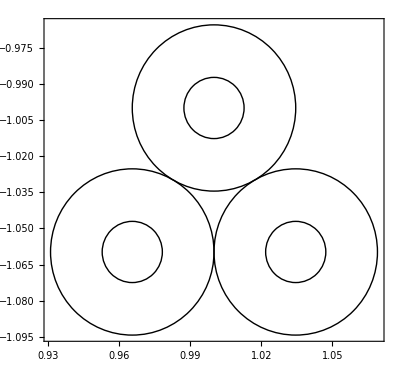

```mathematica
Show[Graphics[mostra],AspectRatio->Automatic,Axes->False,Frame->True,PlotRange->All]
```

S_ij é a distância entre o cabo  i e  j, d é a soma  das profundidades do cabo i para  o cabo j

```mathematica
s13=r4;
s35=s13;
s15=2*s13;
```

Espaçamento dos condutores

```mathematica
d=√((x1-x3)^2+(hc[[1]]-hc[[3]])^2);
Dc=√((x1-x3)^2+(hc[[1]]+hc[[3]])^2);
d15=√((x1-x5)^2+(hc[[1]]-hc[[3]])^2);
Dc15=√((x1-x5)^2+(hc[[1]]+hc[[5]])^2);
```

## Frequências e Inicialização das Listas

### Freqüências de interesse

#### Faixa de Frequência

```mathematica
d1=-1;
d2=N[6.,40];
freqlog[i_,f_,np_]:=Table[N[10^(i+x(f-i)/(Floor[np]-1))],{x,0,np-1}]
freqlin[i_,f_,np_]:=Table[N[(i+x(f-i)/(Floor[np]-1))],{x,0,np-1}]
(*f0=freqlog[d0,d1,500];*)
f1=freqlog[d1,d2,501];
f2=freqlin[10^d1, 10^d2,501];
f=Sort@Join[f2,f1];
nf=Length[f];
```

### Inicialização das listas

```mathematica
T=Table[0,{n,1,nf}];
T1=Table[0,{n,1,nf}];
λ=Table[0,{n,1,nf}];
λ0=Table[0,{n,1,nf}];
Γ1=Table[0,{n,1,nf}];
Yc1=Table[0,{n,1,nf}];
Af1=Table[0,{n,1,nf}];
Am1=Table[0,{n,1,nf}];
γm=Table[0,{n,1,nf}];
```

## Rotinas Auxiliares

### ROT

```mathematica
rot[s_?MatrixQ]:=Module[{S=s,Nc,SA,SB,scale,ang,scale1,col,scale2,err1,err2,numerator,denominator,aaa,bbb,ccc},
Nc=Length[S];
SA=Table[0,{Nc},{Nc}];
SB=SA;
scale1=Table[0,{Nc}];
scale2=scale=ang=scale1;
err1=scale1;
err2=scale1;

numerator=Table[0,{Nc}];
denominator=numerator=scale1=scale2;

For[col=1,col≤ Nc,col++,
numerator[[col]]=0.;
denominator[[col]]=numerator[[col]]=0.;

For[j=1,j≤ Nc,j++,
numerator[[col]]=numerator[[col]]+Im[S[[j,col]]]*Re[S[[j,col]]];
denominator[[col]]=denominator[[col]]+Re[S[[j,col]]]^2-Im[S[[j,col]]]^2];

numerator[[col]]=-2*numerator[[col]];
ang[[col]]=0.5*ArcTan[denominator[[col]],numerator[[col]]];
scale1[[col]]=Cos[ang[[col]]]+ⅈ*Sin[ang[[col]]];
scale2[[col]]=Cos[ang[[col]]+π/2.]+ⅈ*Sin[ang[[col]]+π/2.];

For[j=1,j≤ Nc,j++,
SA[[j,col]]=S[[j,col]]*scale1[[col]];
SB[[j,col]]=S[[j,col]]*scale2[[col]];];

aaa=0.;
bbb=0.;
ccc=0.;

For[j=1,j≤ Nc,j++,
aaa=aaa+Im[SA[[j,col]]]^2;
bbb=bbb+Re[SA[[j,col]]]*Im[SA[[j,col]]];
ccc=ccc+Re[SA[[j,col]]]^2];

err1[[col]]=aaa*Cos[ang[[col]]]^2+bbb*Sin[N[2*ang[[col]],16]]+ccc*Sin[ang[[col]]]^2;

aaa=0.;
bbb=0.;
ccc=0.;

For[j=1,j≤ Nc,j++,
aaa=aaa+Im[SB[[j,col]]]^2;
bbb=bbb+Re[SB[[j,col]]]*Im[SB[[j,col]]];
ccc=ccc+Re[SB[[j,col]]]^2];

err2[[col]]=aaa*Cos[ang[[col]]]^2+bbb*Sin[N[2*ang[[col]],16]]+ccc*Sin[ang[[col]]]^2;

If[err1[[col]]<err2[[col]],scale[[col]]=scale1[[col]],scale[[col]]=scale2[[col]]];

S[[All,col]]=S[[All,col]]*scale[[col]];
];
Return[S]
]
```

```mathematica
func[mat_,j_]:=ReplacePart[mat,Sequence[rep[[j,2]]],rep[[j,1]]]
```

```mathematica
MAC[e1_,e2_]:=With[{e1h=ConjugateTranspose[e1]},e1h.e2]
```

### Roda Autovetores

```mathematica
xchEig[oldT0_,T0_]:=Module[{Q=oldT0,M1=T0,Q1,h1,matrix,in,indice,dum,nc},
nc=Length[Q];
h1=Abs[Re[MAC[M1,Q]]];
matrix=Table[0,{nc},{nc}];
in=Flatten[Table[Position[h1[[i]],Max[h1[[i]]]],{i,nc}]];
indice=Table[{i,in[[i]]},{i,nc}];
rep=Thread[Rule[indice,1]];
R=Fold[func,matrix,Range[nc]];
Q1=M1.R;
(* verifica se há mudança de sinal nos autovetores *)
dum=DiagonalMatrix[Diagonal[Sign[Re[ConjugateTranspose[Q1].Q]] ]];

Q1.dum
]
```

## Principal Loop de Frequência

```mathematica
AbsoluteTiming[Do[{ω=2 π f[[nm]],
ηc=√((ⅉ  ω μ)/ρc),
ηs=√((ⅉ  ω μ)/ρs),
η=√((ⅉ  ω μ)/ρ),
(*-----------Matrix de Admitância-Shunt-------------*)
y1=ⅉ ω 2 π ϵ1/Log[r2/r1],
y2=ⅉ ω 2 π ϵ2/Log[r4/r3],
Ycond={{y1, -y1},{-y1, y1+y2}},
Zero=Table[0,{i,1,2},{j,1,2}],
Ycabo=ArrayFlatten[{{Ycond,Zero,Zero},{Zero,Ycond,Zero},{Zero,Zero,Ycond}}],

(*----------Matriz de Impedância Série--------------*)
z1=(ρc ηc)/(2π r1)BesselI[0,ηc r1]/BesselI[1,ηc r1],
z2=ⅉ(ω μ)/(2π)Log[r2/r1],
z6=ⅉ(ω μ)/(2π)Log[r4/r3],
Den=BesselI[1,ηs r3]BesselK[1,ηs r2]-BesselI[1,ηs  r2]BesselK[1,ηs r3],
z3=(ρs ηs)/(2π r2)1/Den(BesselI[0,ηs r2]BesselK[1, ηs r3]+BesselK[0,ηs  r2]BesselI[1,ηs  r3]),
z4=ρs/(2π r2 r3)1/Den,
z5=(ρs ηs)/(2π r3)1/Den(BesselI[0,ηs r3]BesselK[1, ηs r2]+BesselK[0,ηs r3]BesselI[1,ηs r2]),
z7=ⅉ(ω μ)/(2π)(-Log[(EulerGamma η r4)/2]+1/2-(4η)/3 hc[[1]]),
zsolo1=Table[(ⅉ ω μ)/(2π)(-Log[(EulerGamma η  s13)/2]+1/2-(2η)/3 d),{i,1,2},{j,1,2}],
zsolo2=Table[(ⅉ ω μ)/(2π)(-Log[(EulerGamma η   s15)/2]+1/2-(2η)/3 d),{i,1,2},{j,1,2}],
Zint={{z1+z2+z3+z5+z6+z7-2 z4,z5+z6+z7-z4},{z5+z6+z7-z4,z5+z6+z7}},
Zcabo=ArrayFlatten[{{Zint,zsolo1,zsolo2},{zsolo1,Zint,zsolo1},{zsolo2,zsolo1,Zint}}],

{eval,ev}=Eigensystem[Zcabo.Ycabo],
evect=rot[Transpose[ev]],
k=nm,

If[k>1,
evect=xchEig[evelho,evect];
λ0[[nm]]=Sqrt[Diagonal[Inverse[R].DiagonalMatrix[eval].R]],
λ0[[nm]]=Sqrt[eval];
];

evelho=evect;
Am1[[nm]]=Exp[-λ0[[nm]] compr],
T[[nm]]=evect

(*,

λ0[[nm]]=Sort[Sqrt[eval], (ω/Im[#1])<(ω/Im[#2])&];*)

},{nm,1,nf}]]
```

{4.043045,Null}

```mathematica
Eigenvalues[Zcabo.Ycabo]
```

{-0.150699+0.0160322 ⅈ,-0.013065-0.00540886 ⅈ,-0.00480869-0.00540057 ⅈ,-0.00154876+0.0000113887 ⅈ,-0.00154876+0.0000113887 ⅈ,-0.00154876+0.0000113887 ⅈ}

```mathematica
Eigenvalues[Zcabo.Ycabo-DiagonalMatrix[Table[1,{Length[Zcabo]}]]]+1
```

{-0.150699+0.0160322 ⅈ,-0.013065-0.00540886 ⅈ,-0.00480869-0.00540057 ⅈ,-0.00154876+0.0000113887 ⅈ,-0.00154876+0.0000113887 ⅈ,-0.00154876+0.0000113887 ⅈ}

```mathematica
Sort[Eigenvalues[Zcabo.Ycabo],#1==#2&]
```

{-0.00154876+0.0000113887 ⅈ,-0.00154876+0.0000113887 ⅈ,-0.00154876+0.0000113887 ⅈ,-0.00480869-0.00540057 ⅈ,-0.013065-0.00540886 ⅈ,-0.150699+0.0160322 ⅈ}

### Descruzamento de Autovetores

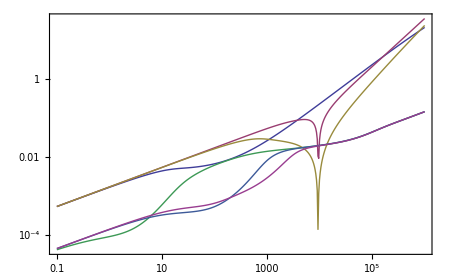

```mathematica
ListLogLogPlot[{
Transpose@{f,1000 Re[λ0[[All,1]]]},
Transpose@{f,1000 Re[λ0[[All,2]]]},
Transpose@{f,1000 Re[λ0[[All,3]]]},
Transpose@{f,1000 Re[λ0[[All,4]]]},
Transpose@{f,1000 Re[λ0[[All,5]]]},
Transpose@{f,1000 Re[λ0[[All,6]]]}
},PlotRange->All]
```

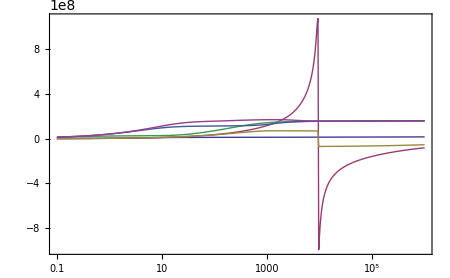

```mathematica
ListLogLinearPlot[{
Transpose@{f,2 π f/Im[λ0[[All,1]]]},
Transpose@{f,2 π f/Im[λ0[[All,2]]]},
Transpose@{f,2 π f/Im[λ0[[All,3]]]},
Transpose@{f,2 π f/Im[λ0[[All,4]]]},
Transpose@{f,2 π f/Im[λ0[[All,5]]]},
Transpose@{f,2 π f/Im[λ0[[All,6]]]}
},PlotRange-> All]
```

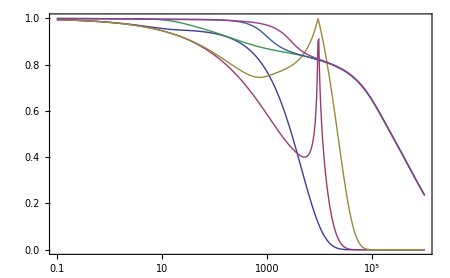

```mathematica
ListLogLinearPlot[{
Transpose@{f,Abs[Am1[[All,1]]]},
Transpose@{f,Abs[Am1[[All,2]]]},
Transpose@{f,Abs[Am1[[All,3]]]},
Transpose@{f,Abs[Am1[[All,4]]]},
Transpose@{f,Abs[Am1[[All,5]]]},
Transpose@{f,Abs[Am1[[All,6]]]}
},PlotRange-> All]
```